## Convection-Diffusion equation

```mathematica
L = 200;
Subscript[l, 1] = 10;
Subscript[l, 2] = 30;
Subscript[l, 11] = 50/3;
Subscript[l, 12] = 20;
Subscript[l, 22]= 70/3;
T = 400;
h = 1;
a = 1;
n = (L - Subscript[l, 1])/h;
profile = 1;
```

```mathematica
Profiles[x_] := 
If[x >= Subscript[l, 1] && x <=  Subscript[l, 2],
{
1/(Subscript[l, 2]-Subscript[l, 1])(x-Subscript[l, 1]), (* Left Triangle *)
1/(Subscript[l, 2] -Subscript[l, 1])(Subscript[l, 2]-x), (* Right Triangle *)
1, (* Rectangle *)
1/2-1/2 Cos[(2 π)/(Subscript[l, 2] - Subscript[l, 1])(x-Subscript[l, 1])], (* Cos *)
If[x < Subscript[l, 11],-2/(3(Subscript[l, 11] - Subscript[l, 1]))(x-Subscript[l, 1]) + 1, 
If[x <= Subscript[l, 22], 1/3, 
2/(3(Subscript[l, 2]-Subscript[l, 22]))(x-Subscript[l, 2]) + 1]
], (* Tooth *)
If[x < Subscript[l, 12], -2/(3(Subscript[l, 12] - Subscript[l, 1]))(x-Subscript[l, 1]) + 1,
2/(3(Subscript[l, 2]-Subscript[l, 12]))(x-Subscript[l, 2])+1](* M *)
},
 {0, 0, 0, 0 , 0 , 0}
]
```

```mathematica
InitialConditions = Table[Profiles[Subscript[l, 1]+i*h], {i, 0, n}] ;
```

```mathematica
Subscript[y0, left] = #⟦1⟧ &/@InitialConditions; u0Left [x_]:= Profiles[x]⟦1⟧;
```

```mathematica
Subscript[y0, right] = #⟦2⟧ &/@InitialConditions; u0Right [x_]:= Profiles[x]⟦2⟧;
```

```mathematica
Subscript[y0, rect] =#⟦3⟧ &/@InitialConditions ; u0Rect [x_]:= Profiles[x]⟦3⟧;
```

```mathematica
Subscript[y0, cos] = #⟦4⟧ &/@InitialConditions; u0Cos [x_]:= Profiles[x]⟦4⟧;
```

```mathematica
Subscript[y0, tooth] = #⟦5⟧ &/@InitialConditions; u0Tooth[x_]:= Profiles[x]⟦5⟧;
Subscript[y0, M] = #⟦6⟧ &/@InitialConditions; u0M [x_]:= Profiles[x]⟦6⟧;
```

```mathematica
y0 = Subscript[y0, tooth]; u0 = u0Tooth;
```

```mathematica
solution = {y0}; print = {Table[{Subscript[l, 1] + i*h, y0⟦i+1⟧}, {i, 0, n}]};
```

```mathematica
γ = 1; τ = (γ h)/Abs[a];
```

```mathematica
For[t = 1, t <= T, t = t + τ,
γ = 1;
values = {0};
If[a > 0, 
For[i = 1, i <= n,++i,
AppendTo[values, (1-γ)solution⟦-1,i+1⟧ + γ solution⟦-1,i⟧]
]; 
AppendTo[solution,values]; 
If[Mod[t, 30] == 0,AppendTo[print,Table[{Subscript[l, 1] + i*h, values⟦i+1⟧}, {i, 0, n}]]],
For[i = n-1, i >= 0,--i,
AppendTo[values, (1-γ)solution⟦-1,i+1⟧ + γ solution⟦-1,i⟧]
]; 
AppendTo[solution,Reverse@values] ; If[Mod[t, 30] == 0, AppendTo[print,Table[{L + i-h, values⟦i+1⟧}, {i, 0, n}]]]
];
];
```

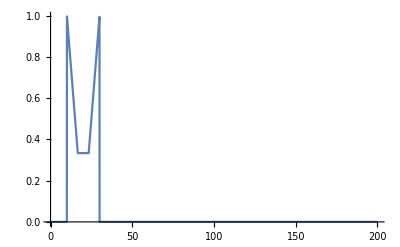

```mathematica
Plot[u0[x], {x, 0, L}]
```

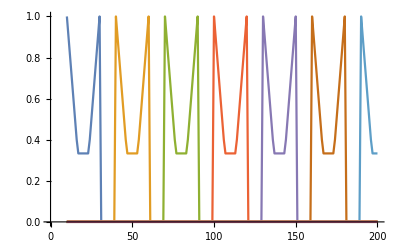

```mathematica
ListLinePlot[print ]
```

```mathematica
δm[cells_List, i_Integer] := Module[
{cond = False,delta =0, min1 = 0, min2 = 0},
If[i<0 || i>Length@cells-1, Return@0];
If[i ==0, 
cond = (cells⟦i+2⟧-cells⟦i+1⟧) > 0; 
delta = 1/2(cells⟦i+2⟧+cells⟦i+1⟧); 
min1 = 2 Abs[cells⟦i+2⟧-cells⟦i+1⟧]; 
min2=0;
Return@If[cond, Sign[delta]Min[{Abs[delta], min1, min2}], 0]
];
If[i == Length@cells-1,
cond =cells⟦i+1⟧-cells⟦i⟧ >0; 
delta = 1/2(cells⟦i+1⟧+cells⟦i⟧); 
 min1 = 0;
 min2 = 2Abs[cells⟦i+1⟧-cells⟦i⟧];
Return@If[cond, Sign[delta]Min[{Abs[delta], min1, min2}], 0];
];
cond = (cells⟦i+2⟧-cells⟦i+1⟧)(cells⟦i+1⟧-cells⟦i⟧) > 0;delta = (cells⟦i+2⟧+cells⟦i⟧)/2; 
min1 = 2 Abs[cells⟦i+2⟧-cells⟦i+1⟧]; 
min2 = 2 Abs[cells⟦i+1⟧-cells⟦i⟧];
Return@If[cond, Sign[delta]Min[{Abs[delta], min1, min2}], 0];
];
```

```mathematica
Δ[cell_List] := Last@cell - First@cell;
```

```mathematica
sixth[cell_List]:= 6(cell⟦-2⟧ - 1/2(Last@cell + First@cell));
```

```mathematica
Adjust[boundaries_List] := Module[
{result = boundaries,cell, delta ,deltaSix, six, deltaSq},
For[i = 1, i < n,++i,
cell = result⟦i+1⟧;
If[(cell⟦3⟧-cell⟦2⟧)(cell⟦2⟧ - cell⟦1⟧) <= 0, cell= {cell⟦2⟧, cell⟦2⟧, cell⟦2⟧}];
delta = Δ[cell]; six = sixth[cell]; deltaSix = delta*six; deltaSq = delta^2;
If[deltaSix > deltaSq, cell⟦1⟧ = 3 cell⟦2⟧ - 2 cell⟦3⟧];
If[deltaSix <-deltaSq,cell⟦3⟧ = 3cell⟦2⟧- 2 cell⟦1⟧];
result⟦i+1⟧ = cell;
];
Return@result;
];
```

## Piecewise Parabolic Method. PPM

```mathematica
solutionPPM = {};
```

```mathematica
For[t = 1, t < Length@solution, ++t,
cells = solution⟦t⟧;
boundaries = {{cells⟦1⟧}};
 For[i = 1, i < n,++i,
boundary = {boundaries⟦-1,-1⟧,cells⟦i+1⟧,1/2(cells⟦i+2⟧ + cells⟦i+1⟧)-1/6(δm[cells, i+1]- δm[cells,i])};
AppendTo[boundaries, boundary];
];
AppendTo[boundaries,{cells⟦n+1⟧}];
AppendTo[solutionPPM, Adjust@boundaries]
];
```

```mathematica
segments={{Subscript[l, 1], Subscript[l, 1]+h/2}}~Join~Table[{Subscript[l, 1]+(i-1/2)h,Subscript[l, 1]+i*h,Subscript[l, 1]+(i+1/2)h}, {i, 1,n-1, 1}]~Join~{{L-h/2, L}};
timestamps=Table[τ j,{j, 0, T}];
```

```mathematica
PPM[x_, t_, integrate_] := Module[
{cell,segment,timestamp, ξ, η},
timestamp = Flatten@Position[timestamps, _?(# == t&)]; If[Length@timestamp==0,Return@0, timestamp = First@timestamp];
If[timestamp>Length@solutionPPM, Return@0];
segment =Flatten@Position[segments, _?((First@# <= x &&Last@# >= x )&)];
If[Length@segment==0, Return@0, segment = First@segment];
If[segment > Length@solutionPPM⟦timestamp⟧, Return@0];
cell = solutionPPM⟦timestamp, segment⟧;
If[integrate,
(* ξ^2 = 1/h^2(x^2 - 2 x segments⟦segment,1⟧ + segments⟦segment,1⟧^2) *)
ξ = 1/h(x^2/2 - x*segments⟦segment,1⟧); η =  1/h^2(x^3/3- x^2 segments⟦segment,1⟧ + x segments⟦segment,1⟧^2);Return[x*First@cell + ξ*Δ[cell] + sixth[cell]*(ξ - η)],
ξ = 1/h(x - segments⟦segment,1⟧); Return[First@cell + ξ(Δ[cell] + sixth[cell](1-ξ))];
];
]
```

First::normal: Nonatomic expression expected at position 1 in First[List].

Last::normal: Nonatomic expression expected at position 1 in Last[List].

First::normal: Nonatomic expression expected at position 1 in First[List].

Last::normal: Nonatomic expression expected at position 1 in Last[List].

First::normal: Nonatomic expression expected at position 1 in First[10].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[10].

General::stop: Further output of Last::normal will be suppressed during this calculation.

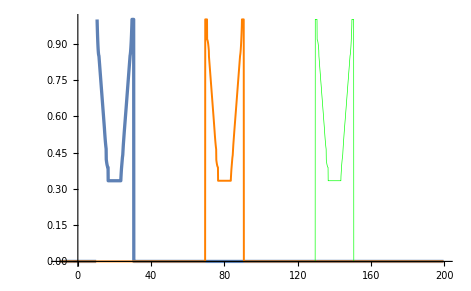

```mathematica
Show[Plot[PPM[x, 0, False], {x, -Subscript[l, 1], L}, PlotStyle->{Thickness -> 0.005}],Plot[PPM[x, 60, False], {x, -Subscript[l, 1], L}, PlotStyle->{Thickness -> 0.003, Orange}], Plot[PPM[x, 120, False], {x,- Subscript[l, 1], L}, PlotStyle->{ Thickness -> 0.001,Green}] ]
```

## Piecewise Parabolic Method On a Local Template. PPML

```mathematica
PPM[30, 0, False] // N
```

First::normal: Nonatomic expression expected at position 1 in First[List].

Last::normal: Nonatomic expression expected at position 1 in Last[List].

First::normal: Nonatomic expression expected at position 1 in First[List].

Last::normal: Nonatomic expression expected at position 1 in Last[List].

First::normal: Nonatomic expression expected at position 1 in First[10].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[10].

General::stop: Further output of Last::normal will be suppressed during this calculation.

1.12917